```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr,getOmegaFromKandDepth,getTFromLandDepth}

```mathematica
(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
filename="data4";
```

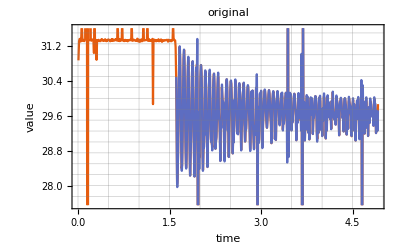

```mathematica
list=Import[FileNameJoin[{NotebookDirectory[],"input_data",filename<>".csv"}]];
interpolated=Import[FileNameJoin[{NotebookDirectory[],"input_data",filename<>"_interpolated.csv"}]];

lastt=list[[-1,1]];
n=Length[list];
freqlist=Table[i/lastt,{i,0,n-1}];
fig=ListPlot[
{list[[2;;,{1,2}]],
interpolated[[2;;,{1,2}]]
},
PlotLabel->"original",
FrameLabel->{"time","value"},
GridLines->All,
Evaluate[plot2Doption]]
```

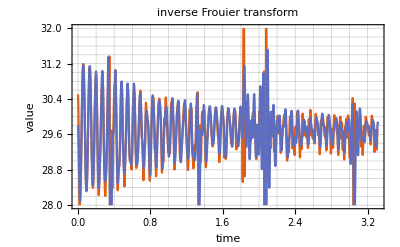

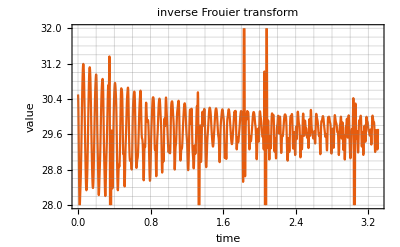
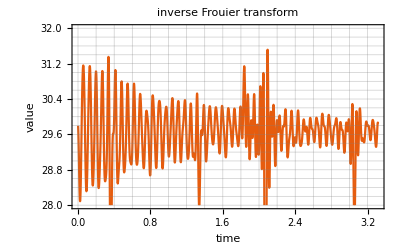

```mathematica
list=Import[FileNameJoin[{NotebookDirectory[],"input_data",filename<>"_invDFT.csv"}]];
data={{#1-interpolated[[1,1]],#2}&@@@interpolated,list[[2;;,{1,2}]]};
fig=ListPlot[data,
PlotLabel->"inverse Frouier transform",
FrameLabel->{"time","value"},
GridLines->All,
PlotRange->{Automatic,30+{-1,1}*2},
Evaluate[plot2Doption]]

fig=ListPlot[#,
PlotLabel->"inverse Frouier transform",
FrameLabel->{"time","value"},
GridLines->All,
PlotRange->{Automatic,30+{-1,1}*2},
Evaluate[plot2Doption]]&/@data
```

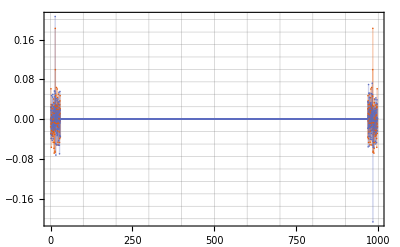

```mathematica
(*list=Table[Cos[2π/n*i]*Cos[5π/n*i],{i,0,n-1,1}];*)
plot2Doption=Append[{PlotRange->All,(*PlotStyle->Red,*)Filling->Axis,GridLines->All,Joined->False},plot2Doption];
list=Import[FileNameJoin[{NotebookDirectory[],"input_data",filename<>"_DFT.csv"}]];
fig=ListPlot[
{{list[[2;;,1]],list[[2;;,2]]}ᵀ,
{list[[2;;,1]],list[[2;;,3]]}ᵀ},
GridLines->All,
 Joined->False,
Evaluate[plot2Doption]]
```